# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
Get["/home/miguel/Desktop/MINIPC/Prethermalization/QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Entanglement

```mathematica
(*2. Parameters*)
L=6;
J=1;
g=2.;
hlist=Sort[Append[Table[10^i,{i,-6,-1,0.5}],0.0]];
tlist=Developer`ToPackedArray[Table[10^i,{i,-1,10,0.0050}]];
tlist//Length
hlist//Length
```

2201

12

```mathematica
states=Table[RandomChainProductState[L],{10}];
```

```mathematica
states=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{100}];
```

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
(*3. Build block maps and compiled fast expander*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
```

```mathematica
(*4. Hamiltonian and evolvers*)
h=hlist[[-1]];
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*5. Distribute*)
DistributeDefinitions[evenMap,oddMap,ProjectBlockVector,ExpandFullStateFast,tlist,L,new,evenEvolver,oddEvolver];
```

```mathematica
(*6. Define worker on all kernels*)
ParallelEvaluate[entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];];
```

```mathematica
(*7. Run computation*)
AbsoluteTiming[data=ParallelTable[entanglementWorker[state],{state,states}];]
```

{0.355555,Null}

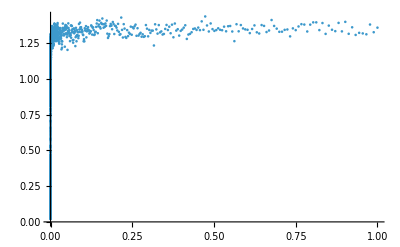

```mathematica
ListPlot[Transpose[{tlist,Mean[data]}],PlotRange->All]
```

## Exporting files

```mathematica
(* ===0) OUTPUT FOLDER+HELPERS (add this BEFORE the Do loop)===*)
outDir=FileNameJoin[{NotebookDirectory[],"SRN_entropies"}];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
(*file-safe tag for h values,e.g.0.001->"h_0p001"*)
hTag[h_?NumericQ]:="h_"<>StringReplace[ToString@NumberForm[h,{Infinity,10}],{"."->"p","-"->"m"," "->""}];
(*metadata to write once at the end*)
runMeta=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"tlist"->tlist,"NumStates"->Length[states],"TimestampStart"->DateString[{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}],"WolframVersion"->$Version|>;
(*optional:keep a small per-h timing log*)
perHLog=Association[];
(*safe numeric tag for g (unchanged if you already added it)*)
gTag[x_?NumericQ]:=Module[{d=IntegerString[Floor[FractionalPart[x]*10^4+0.5],10,4]},"1p"<>d];
(*filename base using the INDEX ih,zero-padded to 2 digits*)
baseNameIdx[ih_Integer?Positive]:=StringJoin["SRN_entropies_","L",ToString[L],"_","J",ToString[J],"_","g",gTag[g],"_","h_",IntegerString[ih,10,2]  (*i01,i02,...*)];
```

```mathematica
results={};
Do[
Print["Computing for h = "<>ToString[hlist[[ih]]]];
h=hlist[[ih]];
(*Your step 4:Hamiltonian and evolvers (UNCHANGED)*)Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[1]]];
{oddEigvals,oddEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[2]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*Local (non-parallel) worker using the evolvers for THIS h—UNCHANGED*)entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];
(* ===Only addition:time+export per h===*)
{dt,currentResults}=AbsoluteTiming[ParallelTable[entanglementWorker[state],{state,states}]];
AppendTo[results,currentResults];
perHLog[h]=<|"Seconds"->dt,"ResultShape"->Dimensions[currentResults]|>;
(*build trajectories:one {t,S(t)} table per state*)
trajectories=Map[Transpose[{tlist,#}]&,currentResults];
Export[FileNameJoin[{outDir,baseNameIdx[ih]<>".mx"}],trajectories,"MX"];

,{ih,Length[hlist]}];

(* ===Write metadata once at the end===*)
runMetaFinal=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"NumStates"->Length[states],"PerHFiles"->AssociationThread[hlist,Table[baseNameIdx[i]<>".mx",{i,Length[hlist]}]]|>;
metadata=runMetaFinal;
Put[metadata,FileNameJoin[{outDir,"metadata.m"}]];
Print["Saved per-h .mx files and metadata.m to: ",outDir];
```

Computing for h = 0.

Computing for h =      -6
1. 10

Computing for h =           -6
3.16228 10

Computing for h = 0.00001

Computing for h = 0.0000316228

Computing for h = 0.0001

Computing for h = 0.000316228

Computing for h = 0.001

Computing for h = 0.00316228

Computing for h = 0.01

Computing for h = 0.0316228

Computing for h = 0.1

Saved per-h .mx files and metadata.m to: C:\Users\Miguel\Github\Entropy\Prethermalization\Late time ensembles\SRN_entropies

```mathematica
data=results;
```

```mathematica
plotsa={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[N[J]]<>", g = "<>ToString[N[g]]<>", h = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]},PlotRange->{All,{0,1}}];
AppendTo[plotsa,ploten];
,{h,Length[hlist]}];
```

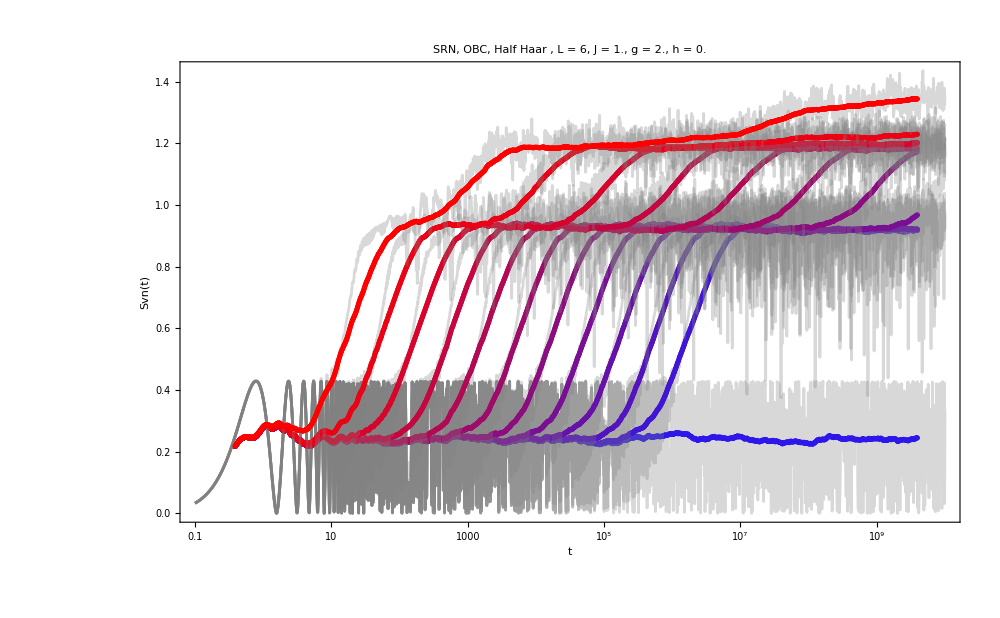

```mathematica
Show[plotsa,PlotRange->All]
```

# Improvement

```mathematica
ClearAll["Global`*"];
(*---HAMILTONIAN---*)
(*Standard Tilted Ising:h*Sx (Transverse)+g*Sz (Longitudinal)*)
(*Note:variable names match your specific usage (g=Longitudinal,h=Transverse)*)
Clear[getHamiltonian];
getHamiltonian[n_,g_,h_]:=Module[{sx,sz,id,H,op},sx=SparseArray[{{0,1},{1,0}}];
sz=SparseArray[{{1,0},{0,-1}}];
id=IdentityMatrix[2,SparseArray];
op[mat_,i_]:=KroneckerProduct@@ReplacePart[ConstantArray[id,n],i->mat];
H=SparseArray[{},{2^n,2^n}];
Do[H-=op[sz,i].op[sz,Mod[i,n]+1],{i,1,n}];(*Interaction ZZ*)Do[H-=h*op[sx,i],{i,1,n}];(*Transverse X*)Do[H-=g*op[sz,i],{i,1,n}];(*Longitudinal Z*)H];

Clear[getPuritySum];
getPuritySum[stateVec_,nSys_]:=Module[{puritySum=0,sub,mat,sv,dim=2^nSys,k,perm,tensor,tensorPerm,half=Floor[nSys/2],val},(*Iterate only through subsets up to size N/2*)
Do[k=Length[sub];
(*Case 0:Empty/Full System->Purity=1*)
If[k==0,puritySum+=2;(*Adds 1 for empty,1 for full*)Continue[]];
(*Prepare Matrix for SVD*)perm=Join[sub,Complement[Range[nSys],sub]];
tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]];
tensorPerm=Transpose[tensor,perm];
mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
(*Compute Purity*)sv=SingularValueList[mat];
val=Total[Chop[sv]^4];
puritySum+=val;,{sub,Subsets[Range[nSys]]}];puritySum];
```

```mathematica
DistributeDefinitions[getPuritySum];
(*---EVOLUTION ENGINE---*)
Clear[runEvolutionForG];
runEvolutionForG[nSys_,gVal_,hVal_,psi0_,tList_]:=Module[{H,evals,evecs,c,evolutionFunc},
(*1. Diagonalize Locally (Fast for N=10)*)
H=getHamiltonian[nSys,gVal,hVal];
{evals,evecs}=Eigensystem[N[H]];
c=Conjugate[evecs].psi0;
DistributeDefinitions[evals,evecs,c,nSys];
evolutionFunc=Function[{t},Module[{psit,sumP},psit=Transpose[evecs].(c*Exp[-I*evals*t]);
sumP=getPuritySum[psit,nSys];
{t,Log[6*Pi]-Log[sumP]/nSys}]];
ParallelMap[evolutionFunc,tList]];
```

```mathematica
(* ==========================================*)
(*2. EXECUTION SCRIPT*)
(* ==========================================*)
(*Parameters*)
Nval=5;
hFixed=0.2; 
tlist=Table[10^i,{i,-1,12,0.005}];
tlist//Length
```

2601

```mathematica
(*The Sweep:Logarithmic g from 10^-8 to 10^-1*)
glist=Table[10^i,{i,-8,-1,0.25}];
glist//Length
```

29

```mathematica
(*Initial State:Random Chain Product State*)
(*Helper to generate random product state|r1>|r2>...*)
psi0=RandomChainProductState[Nval];
```

```mathematica
Print["Running Sweep for N=",Nval," over ",Length[glist]," values of g..."];

(*MAIN LOOP*)
allData=Association[];
Monitor[Do[Print["Processing g = ",NumberForm[g,{2,8}]];
(*Run Calculation*)
(*result=runEvolutionForG[Nval,g,hFixed,psi0,tlist];*)
result=runEvolutionForG[Nval,g,hFixed,psi0,tlist];
(*Store in Association*)
AssociateTo[allData,g->result];,{g,glist}],
Row[{"Current g: ",NumberForm[g,{2,8}]}]];

(*Export Data safely*)
Export["EntropySweep_Data_LRN.mx",allData];
Print["Done! Data exported to Entropy Data"];
```

Running Sweep for N=5 over 29 values of g...

Processing g = 1.00000000×10^-8

Processing g = 1.80000000×10^-8

Processing g = 3.20000000×10^-8

Processing g = 5.60000000×10^-8

Processing g = 1.00000000×10^-7

Processing g = 1.80000000×10^-7

Processing g = 3.20000000×10^-7

Processing g = 5.60000000×10^-7

Processing g = 1.00000000×10^-6

Processing g = 1.80000000×10^-6

Processing g = 3.20000000×10^-6

Processing g = 5.60000000×10^-6

Processing g = 0.00001000

Processing g = 0.00001800

Processing g = 0.00003200

Processing g = 0.00005600

Processing g = 0.00010000

Processing g = 0.00018000

Processing g = 0.00032000

Processing g = 0.00056000

Processing g = 0.00100000

Processing g = 0.00180000

Processing g = 0.00320000

Processing g = 0.00560000

Processing g = 0.01000000

Processing g = 0.01800000

Processing g = 0.03200000

Processing g = 0.05600000

Processing g = 0.10000000

Done! Data exported to Entropy Data

```mathematica
(* ==========================================*)
(*3. VISUALIZATION*)
(* ==========================================*)
(*Create Colors:Blue (Low g)->Red (High g)*)
colors=Table[Blend[{Blue,Red},Rescale[Log10[g],{Min[Log10[glist]],Max[Log10[glist]]}]],{g,glist}];
(*Generate Plot Legends*)
legends=SwatchLegend[colors,ScientificForm[#,2]&/@glist,LegendLabel->"g (Longitudinal)"];
```

```mathematica
allData=Import["/home/miguel/Desktop/MINIPC/Prethermalization/EntropySweep_Data.mx"];
```

```mathematica
allData//Dimensions
```

{29}

```mathematica
(* ==========================================*)(*3. VISUALIZATION WITH MOVING AVERAGE& COLOR BAR*)(* ==========================================*)(*1. Generate Gradient Colors*)
minLog=Min[Log10[glist]];
maxLog=Max[Log10[glist]];
(*2. Process Data for Plotting*)
plotData=Flatten[Table[raw=allData[g];
avg=MovingAverage[raw,50];
(*Normalized position for color*)
normG=Rescale[Log10[g],{minLog,maxLog}];
c=Blend[{Blue,Red},normG];
{(*Curve 1:Raw Data (Thin,Transparent)*)
Style[raw,Thin,Opacity[0.06],Gray],
(*Curve 2:Moving Average (Thick,Solid)*)
Style[avg,Thickness[0.004],c]},{g,glist}]];
```

```mathematica
(*3. Create Color Bar Legend (FIXED)*)
customTicks=Table[{i,Style[Superscript[10,i],15,Black]},{i,minLog,maxLog,1}];
barLegend=BarLegend[{Blend[{Blue,Red},#]&,{minLog,maxLog}},Ticks->customTicks,LegendLabel->Style["Longitudinal Field g",18,Black],LegendMarkerSize->300,LabelStyle->{Black,15} ,Background->White];
```

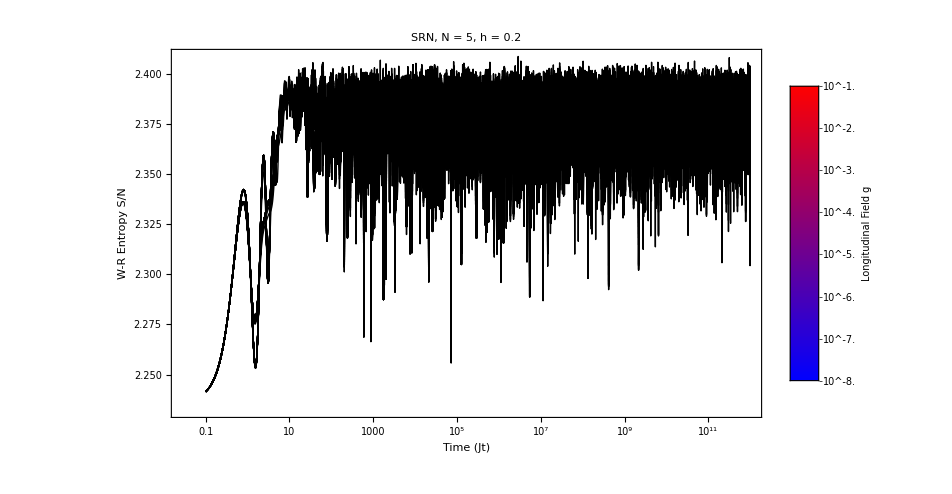

```mathematica
(*4. Final Plot*)
plot=ListLogLinearPlot[plotData,PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],(*Labels*)FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["SRN, N = "<>ToString[Nval]<>", h = "<>ToString[hFixed],22,Black],(*Options*)ImageSize->800,Joined->True,PlotLegends->Placed[barLegend,Right],Background->White]
```

```mathematica
Export["test.png",plot]
```

test.png

# Individual purities, LRN

```mathematica
(*0. Setup*)ClearAll["Global`*"];
(*---HAMILTONIAN (Same as before)---*)
Clear[getHamiltonian];
getHamiltonian[n_,g_,h_]:=Module[{sx,sz,id,H,op},sx=SparseArray[{{0,1},{1,0}}];
sz=SparseArray[{{1,0},{0,-1}}];
id=IdentityMatrix[2,SparseArray];
op[mat_,i_]:=KroneckerProduct@@ReplacePart[ConstantArray[id,n],i->mat];
H=SparseArray[{},{2^n,2^n}];
Do[H-=op[sz,i].op[sz,Mod[i,n]+1],{i,1,n}];(*Interaction ZZ*)Do[H-=h*op[sx,i],{i,1,n}];(*Transverse X*)Do[H-=g*op[sz,i],{i,1,n}];(*Longitudinal Z*)H];
(*---NEW:PARTITIONED PURITY FUNCTION---*)
(*Returns a list:{SumPurity_k1,SumPurity_k2,...,SumPurity_k(N/2)}*)
getPurityPartitioned[stateVec_,nSys_]:=Module[{counts=ConstantArray[0.0,Floor[nSys/2]],(*Storage for k=1 to N/2*)sub,k,perm,tensor,tensorPerm,mat,sv,val},(*Loop over ALL subsets*)
Do[k=Length[sub];
(*We only care about sizes 1 to N/2. Use symmetry P(A)=P(A_complement) to handle k>N/2 if needed,but iterating Subsets covers A and A^c naturally.*)(*Map k to index 1..N/2*)(*If k is 1 or N-1->Index 1*)(*If k is 2 or N-2->Index 2*)
effectiveK=If[k>nSys/2,nSys-k,k];
If[effectiveK>0,perm=Join[sub,Complement[Range[nSys],sub]];
tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]];
tensorPerm=Transpose[tensor,perm];
(*Note:We use original k for reshaping to keep matrix dimensions consistent with perm*)
mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
sv=SingularValueList[mat];
val=Total[Chop[sv]^4];
(*Accumulate*)
counts[[effectiveK]]+=val;];
,{sub,Subsets[Range[nSys]]}];
counts];
DistributeDefinitions[getPurityPartitioned];
```

```mathematica
(*---EVOLUTION ENGINE (Partitioned)---*)
runDetailedEvolution[nSys_,g_,h_,psi0_,tlist_]:=Module[{H,evals,evecs,c,evolutionFunc},
Print["1. Constructing Hamiltonian (N=",nSys,")..."];
H=getHamiltonian[nSys,g,h];
Print["2. Diagonalizing..."];
{evals,evecs}=Eigensystem[N[H]];
c=Conjugate[evecs].psi0;
Print["3. Distributing to Kernels..."];
DistributeDefinitions[evals,evecs,c,nSys];
(*Worker Function:Returns {t,{SumP_1,SumP_2,...}}*)
evolutionFunc=Function[{t},Module[{psit,parts},
psit=Transpose[evecs].(c*Exp[-I*evals*t]);
parts=getPurityPartitioned[psit,nSys];
{t,parts}]];
Print["4. Running Parallel Evolution..."];
ParallelMap[evolutionFunc,tlist]];
```

```mathematica
(*---PARAMETERS---*)
Nval=12;
(*Initial State:Product State*)
psi0=Normal[Flatten[KroneckerProduct@@Table[{1,0},{Nval}]]]; (* |00...0>*)
psi0=RandomChainProductState[Nval];
```

```mathematica
(*Time Grid*)
tlist=Table[10^i,{i,-1,10,0.0010}];
tlist//Length
```

11001

```mathematica
g=0.0001; (*Strong longitudinal field breaks integrability*)
h=1.05;
```

```mathematica
(*EXECUTE*)
Print["Starting Detailed Run..."];
detailedData=runDetailedEvolution[Nval,g,h,psi0,tlist];
Print["Done."];
```

Starting Detailed Run...

1. Constructing Hamiltonian (N=12)...

2. Diagonalizing...

Eigensystem::arh: Because finding 4096 out of the 4096 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

3. Distributing to Kernels...

4. Running Parallel Evolution...

Done.

```mathematica
(*1. Retrieve and Validate Data*)
times=detailedData[[All,1]];
rawSums=detailedData[[All,2]];
(*2. Auto-Detect System Size from Data*)
(*The data contains partitions up to Floor[N/2].*)
(*Length[rawSums[[1]]] tells us exactly how many partitions exist.*)
numPartitions=Length[rawSums[[1]]];
detectedN=2*numPartitions; (*Approximation assuming even N*)
Print["Detected data for N = ",detectedN," (",numPartitions," partition sizes)."];
(*3. Define Normalization Factors based on DETECTED size*)
normalizationFactors=Table[If[k<detectedN/2,2*Binomial[detectedN,k],(*Size k and N-k (Double Counted)*)Binomial[detectedN,k]      (*Size N/2 (Single Counted)*)],{k,1,numPartitions}];
(*4. Calculate Average Entropy*)
entropyData=Table[currentSums=rawSums[[tIndex]];
Table[(*Safe division*)avgPurity=currentSums[[k]]/normalizationFactors[[k]];
-Log[avgPurity],{k,1,numPartitions}],{tIndex,1,Length[times]}];
(*5. Visualization*)
curves=Table[{timeData=Transpose[{times,entropyData[[All,k]]}],(*Color coding:Blue (k=1) to Red (k=max)*)color=ColorData["Rainbow"][Rescale[k,{1,numPartitions}]]},{k,1,numPartitions}];
```

Detected data for N = 12 (6 partition sizes).

```mathematica
(*1. Setup Sorting for Legend (Highest Size on Top)*)
numPartitions=Length[curves];
kValues=Range[numPartitions,1,-1]; (*Descending:N/2 down to 1*)
(*2. Create the Legend*)
plotLegend=SwatchLegend[(*Legend Colors (Sorted Descending)*)Table[ColorData["Rainbow"][Rescale[k,{1,numPartitions}]],{k,kValues}],(*Legend Labels (Sorted Descending)*)Table["Bipartition "<>ToString[k],{k,kValues}],LegendLabel->"Subsystem Size",LegendMarkerSize->20];
```

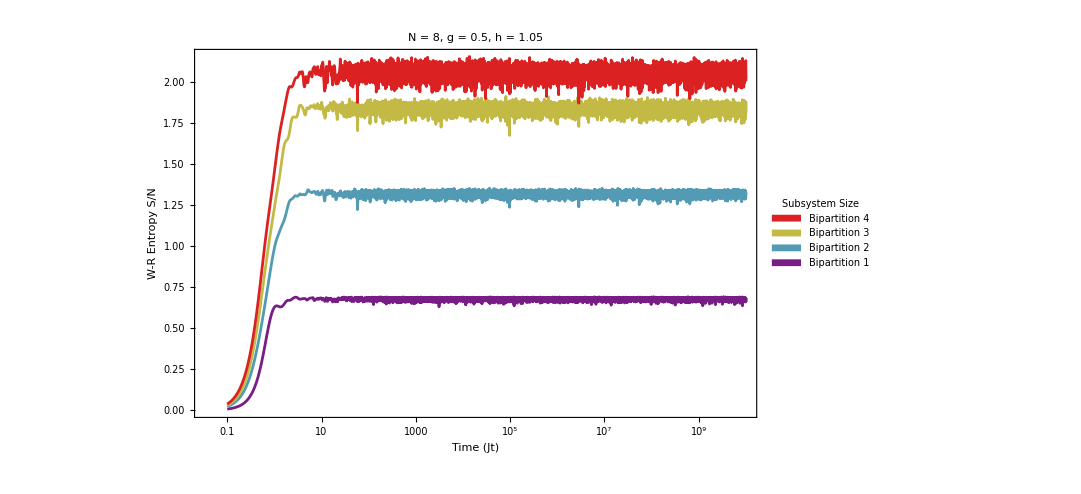

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

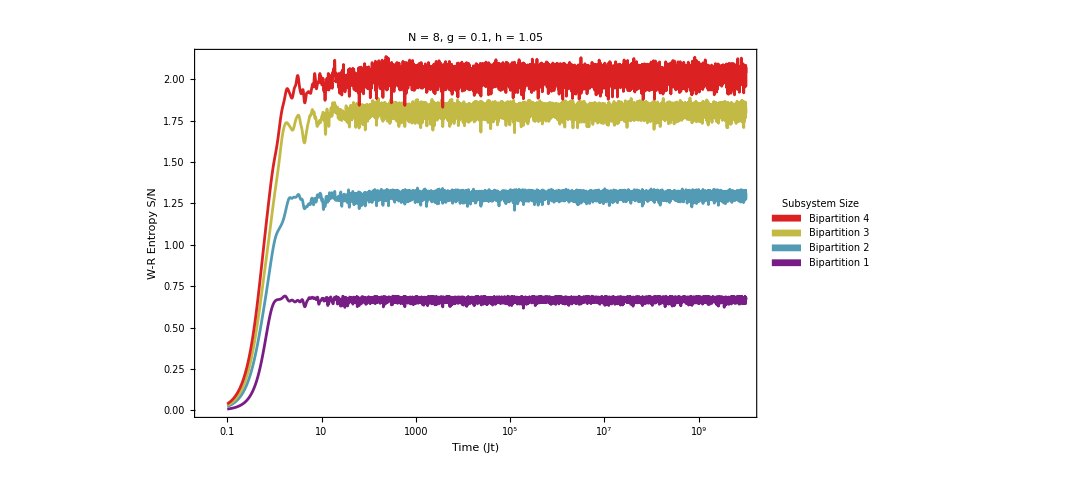

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

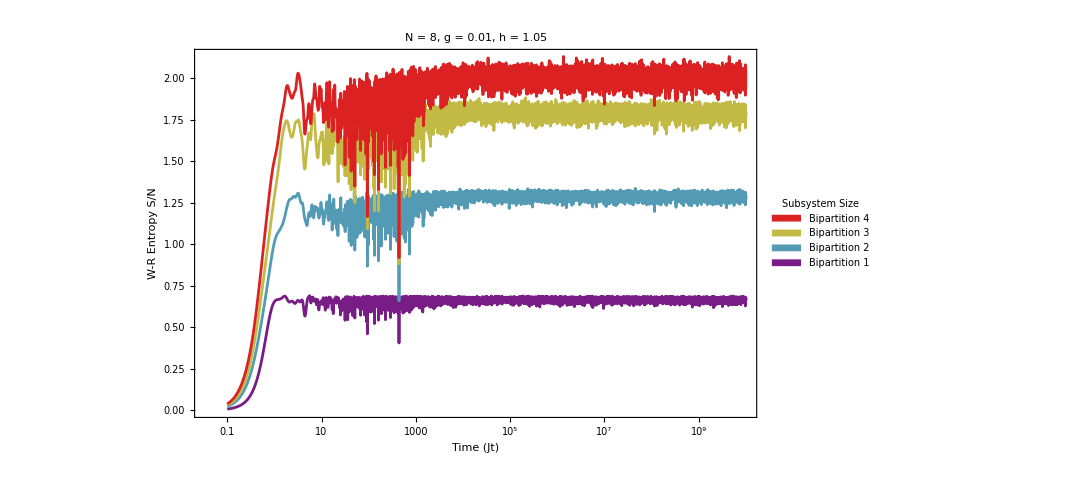

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

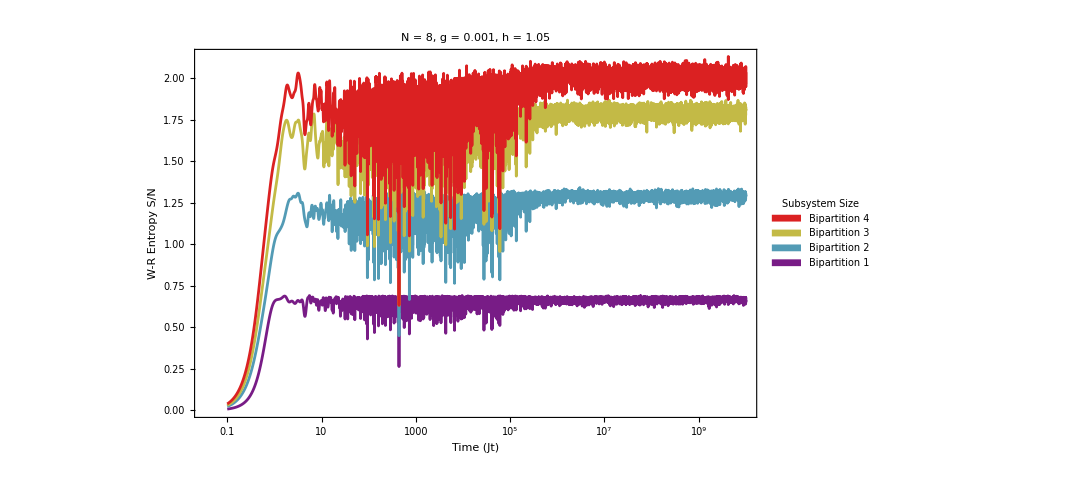

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

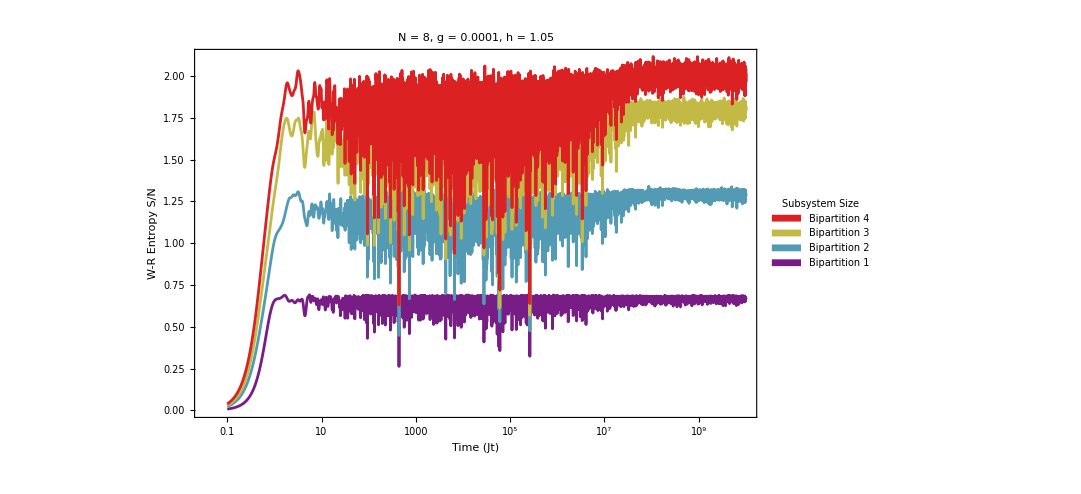

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

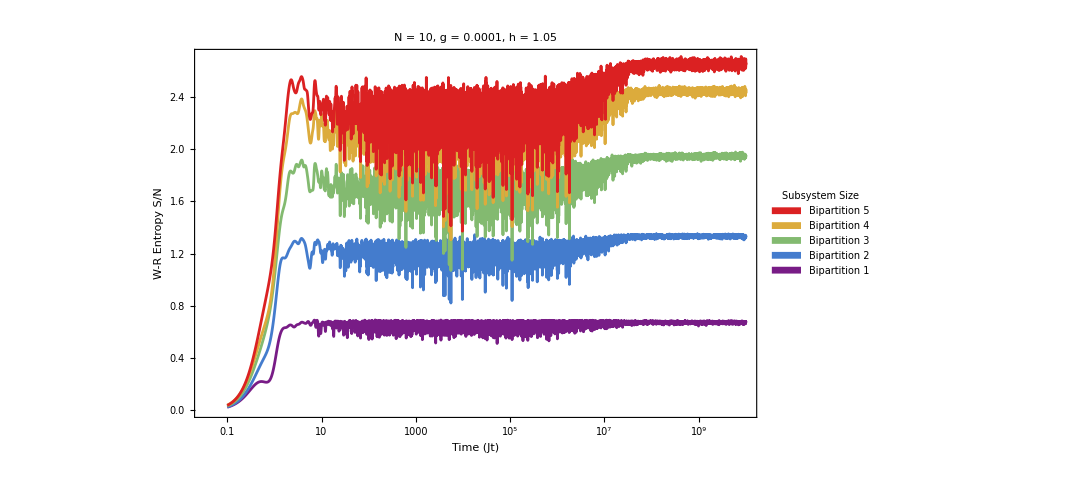

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

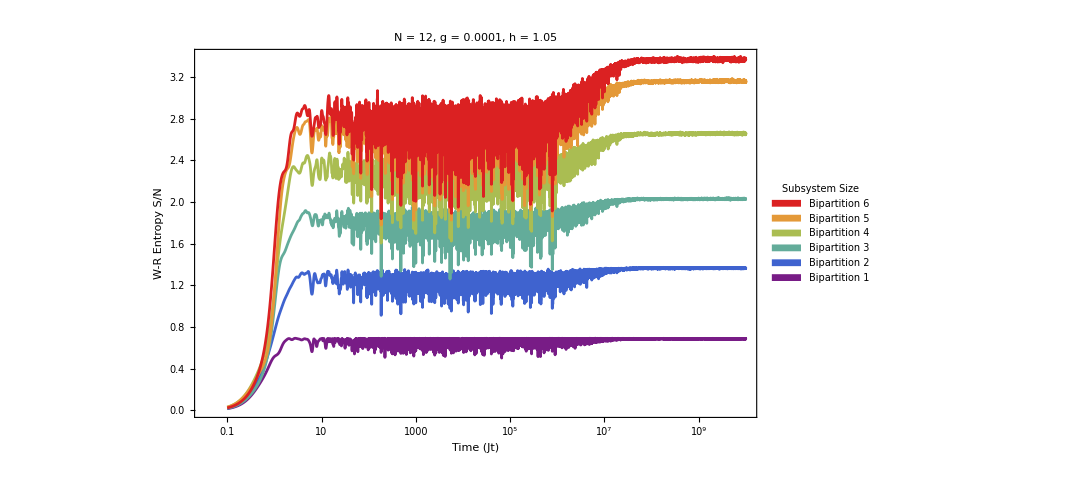

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

## SRN

```mathematica
(*---PARAMETERS---*)
Nval=10;
(*Initial State:Product State*)
psi0=Normal[Flatten[KroneckerProduct@@Table[{1,0},{Nval}]]]; (* |00...0>*)
psi0=RandomChainProductState[Nval];
```

```mathematica
(*Time Grid*)
tlist=Table[10^i,{i,-1,10,0.0010}];
tlist//Length
```

11001

```mathematica
g=1.0; (*Strong longitudinal field breaks integrability*)
h=0.0001;
```

```mathematica
(*EXECUTE*)
Print["Starting Detailed Run..."];
detailedData=runDetailedEvolution[Nval,g,h,psi0,tlist];
Print["Done."];
```

Starting Detailed Run...

1. Constructing Hamiltonian (N=10)...

2. Diagonalizing...

Eigensystem::arh: Because finding 1024 out of the 1024 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

3. Distributing to Kernels...

4. Running Parallel Evolution...

Done.

```mathematica
(*1. Retrieve and Validate Data*)
times=detailedData[[All,1]];
rawSums=detailedData[[All,2]];
(*2. Auto-Detect System Size from Data*)
(*The data contains partitions up to Floor[N/2].*)
(*Length[rawSums[[1]]] tells us exactly how many partitions exist.*)
numPartitions=Length[rawSums[[1]]];
detectedN=2*numPartitions; (*Approximation assuming even N*)
Print["Detected data for N = ",detectedN," (",numPartitions," partition sizes)."];
(*3. Define Normalization Factors based on DETECTED size*)
normalizationFactors=Table[If[k<detectedN/2,2*Binomial[detectedN,k],(*Size k and N-k (Double Counted)*)Binomial[detectedN,k]      (*Size N/2 (Single Counted)*)],{k,1,numPartitions}];
(*4. Calculate Average Entropy*)
entropyData=Table[currentSums=rawSums[[tIndex]];
Table[(*Safe division*)avgPurity=currentSums[[k]]/normalizationFactors[[k]];
-Log[avgPurity],{k,1,numPartitions}],{tIndex,1,Length[times]}];
(*5. Visualization*)
curves=Table[{timeData=Transpose[{times,entropyData[[All,k]]}],(*Color coding:Blue (k=1) to Red (k=max)*)color=ColorData["Rainbow"][Rescale[k,{1,numPartitions}]]},{k,1,numPartitions}];
```

Detected data for N = 10 (5 partition sizes).

```mathematica
(*1. Setup Sorting for Legend (Highest Size on Top)*)
numPartitions=Length[curves];
kValues=Range[numPartitions,1,-1]; (*Descending:N/2 down to 1*)
(*2. Create the Legend*)
plotLegend=SwatchLegend[(*Legend Colors (Sorted Descending)*)Table[ColorData["Rainbow"][Rescale[k,{1,numPartitions}]],{k,kValues}],(*Legend Labels (Sorted Descending)*)Table["Bipartition "<>ToString[k],{k,kValues}],LegendLabel->"Subsystem Size",LegendMarkerSize->20];
```

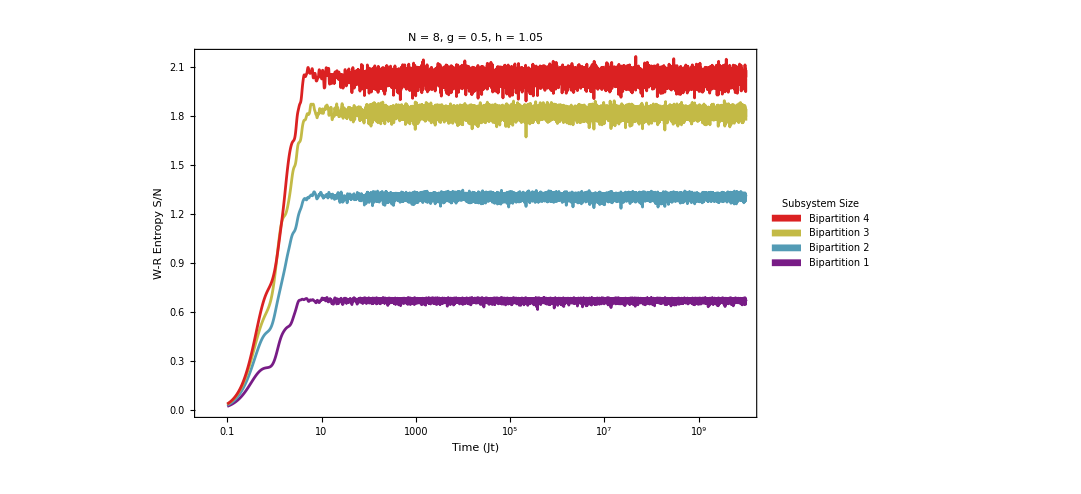

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

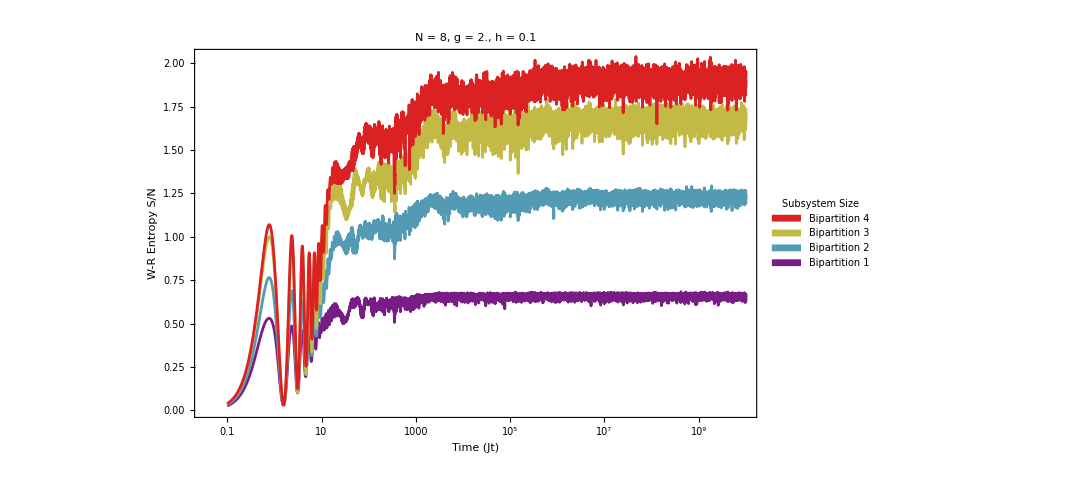

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

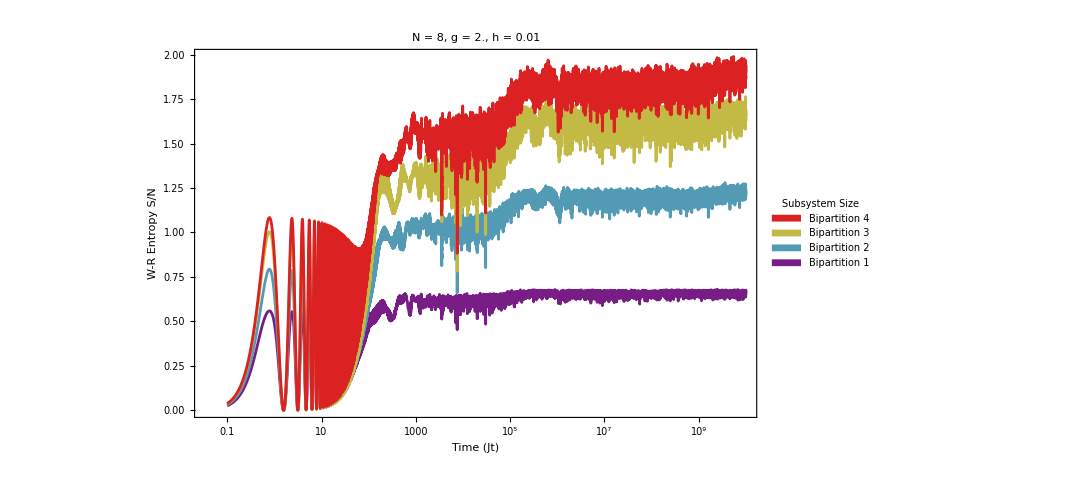

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

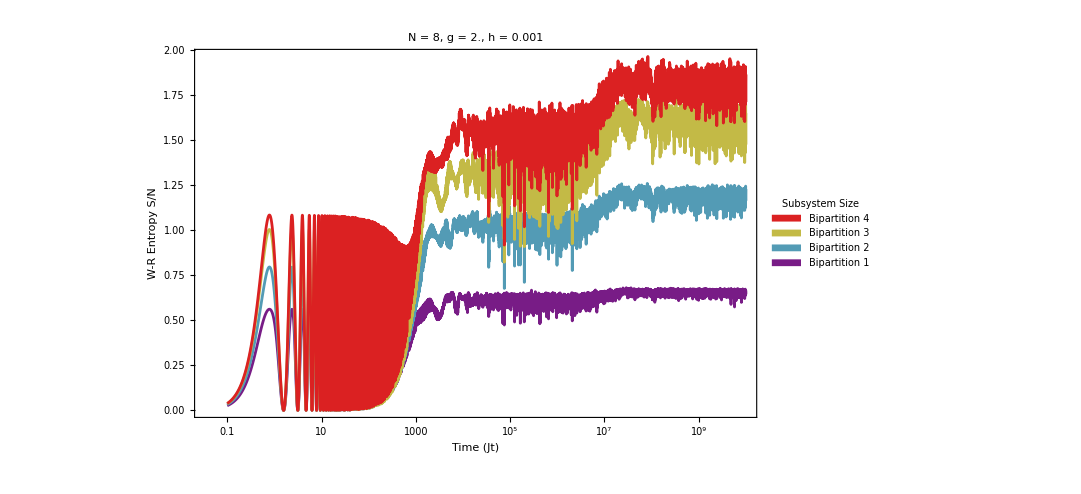

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

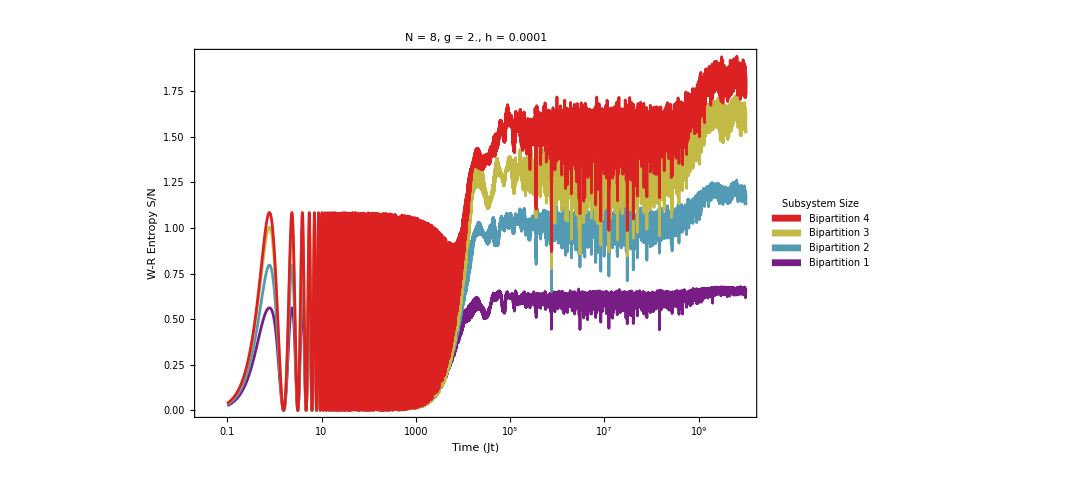

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

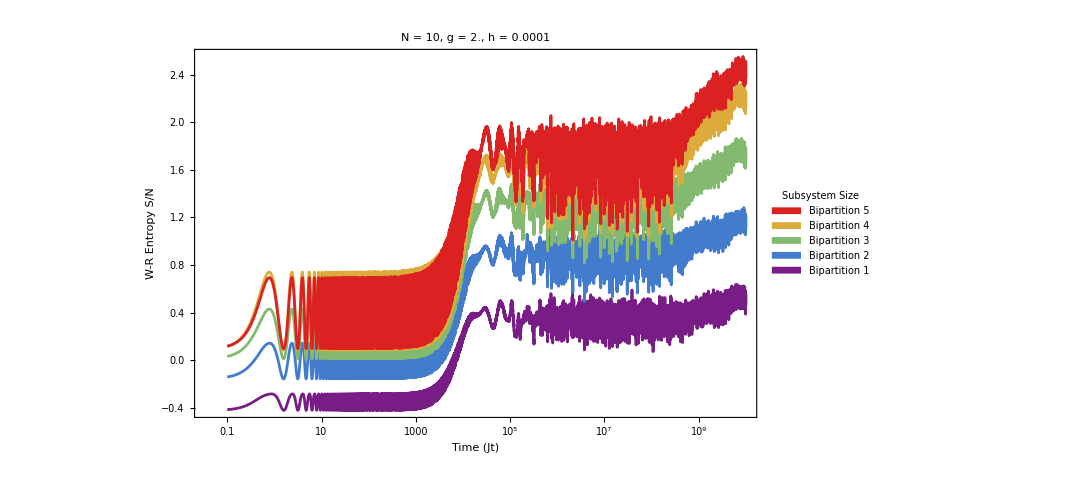

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```

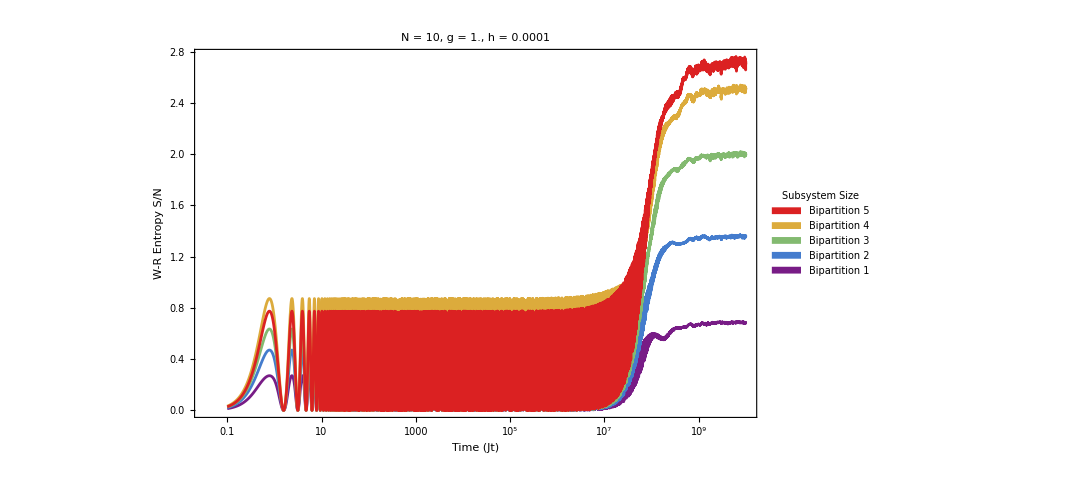

```mathematica
(*3. Plot with Explicit Styles*)
ListLogLinearPlot[curves[[All,1]],(*The Data*)(*CRITICAL FIX:You must tell the plot to use the colors from'curves'*)PlotStyle->curves[[All,2]],PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],Log[4*Pi]}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],PlotLabel->Style["N = "<>ToString[Nval]<>", g = "<>ToString[g]<>", h = "<>ToString[h],20,Black],ImageSize->800,Joined->True,Background->White,(*Attach the Legend*)PlotLegends->Placed[plotLegend,Right]]
```